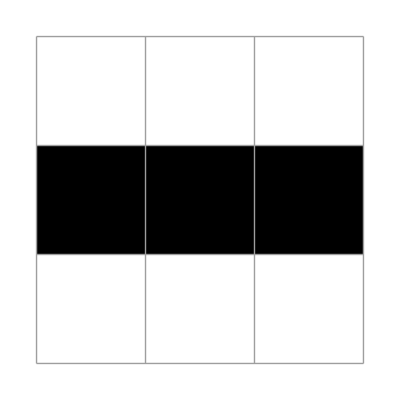
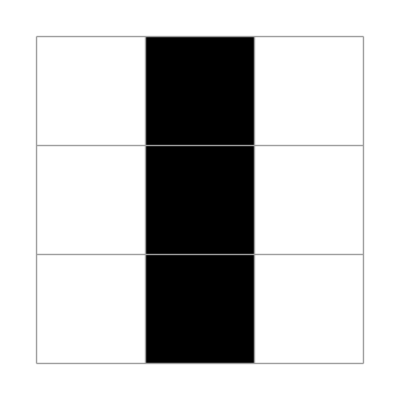

```mathematica
X1=({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}});
plt/@NestList[updateLife[{3,3}][ #]&,
X1,1]
```

```mathematica
Clear[i];
updateLife2[stateXt_]:=Module[
{x,xNW,xN,xNE,xW,xE,xSW,xS,xSE,xPrime,pad,Xt},

pad=ArrayPad[#,1]&;
Table[
Xt=pad[stateXt];
x=Xt[[i,j]];
xNW=Xt[[i+1,j-1]];
xN=Xt[[i+1,j]];
xNE=Xt[[i+1,j+1]];
xW=Xt[[i,j-1]];
xE=Xt[[i,j+1]];
xSW=Xt[[i-1,j-1]];
xS=Xt[[i-1,j]];
xSE=Xt[[i-1,j+1]];
xPrime=Boole[2<xNW+xN+xNE+xW+1/2 x+xE+xSW+xS+xSE<4]
,{i,2,4}
,{j,2,4}
]
] ;
updateLife2[({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}})]
```

{{0,1,0},{0,1,0},{0,1,0}}